# QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Geometric floquet\\QKT_full.wl"];
```

```mathematica
LaunchKernels[14];
```

## Method

```mathematica
(*Floquet parameters*)
J=1001;
d=2 J+1;
α=Pi/2.;
k=10.;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.547927,0.401647}

```mathematica
phases=Sort[Arg[eigenvalm]];
data=Table[{phases[[i]],i},{i,1,Length[phases]}];
```

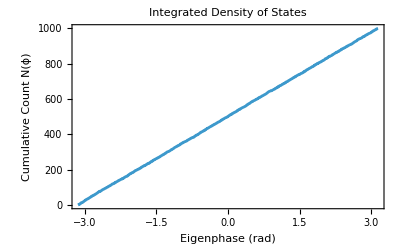

```mathematica
(*3. Plot the staircase function*)
ListPlot[data,Frame->True,FrameLabel->{"Eigenphase (rad)","Cumulative Count N(ϕ)"},PlotLabel->"Integrated Density of States",Joined->True]
```

```mathematica
phases=Sort[Arg[eigenvalM]];
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
poisson[s_]:=Exp[-s];
wignerDyson[s_]:=(Pi*s/2)*Exp[-(Pi*s^2)/4];
```

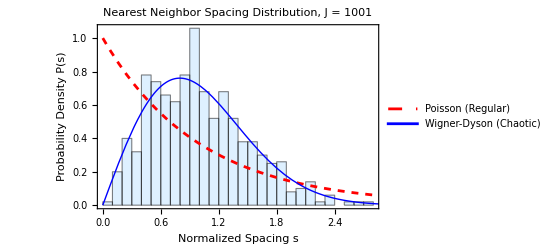

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

## Average energy

```mathematica
(*Floquet parameters*)
J=100;
τ=1;
α=Pi/2.;
k=1.3;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
(*F[α_,k_] := U0[α].Uk[ k];*)
F[α_,k_] := Uk[k].U0[α];
```

```mathematica
Clear[mat];
mat=F[α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

```mathematica
Clear[V];
V[α_,k_]:=(k/(2J))ConjugateTranspose[U0[α]].ops[[4]].U0[α]+α*ops[[3]];
```

```mathematica
Vop=V[α,k];
```

```mathematica
ae=(1/J)Chop[Map[#.Vop.ConjugateTranspose[#]&,neweigenvec]];
```

```mathematica
szM=(Vop)[[1;; ;;2,1;; ;;2]];
szm=(Vop)[[2;; ;;2,2;; ;;2]];
(*Compute expected values of Sz for each eigenvector*)
szExpectationsM=(1/J)Map[#.szM.ConjugateTranspose[#]&,eigenvecM];
szExpectationsm=(1/J)Map[#.szm.ConjugateTranspose[#]&,eigenvecm];
```

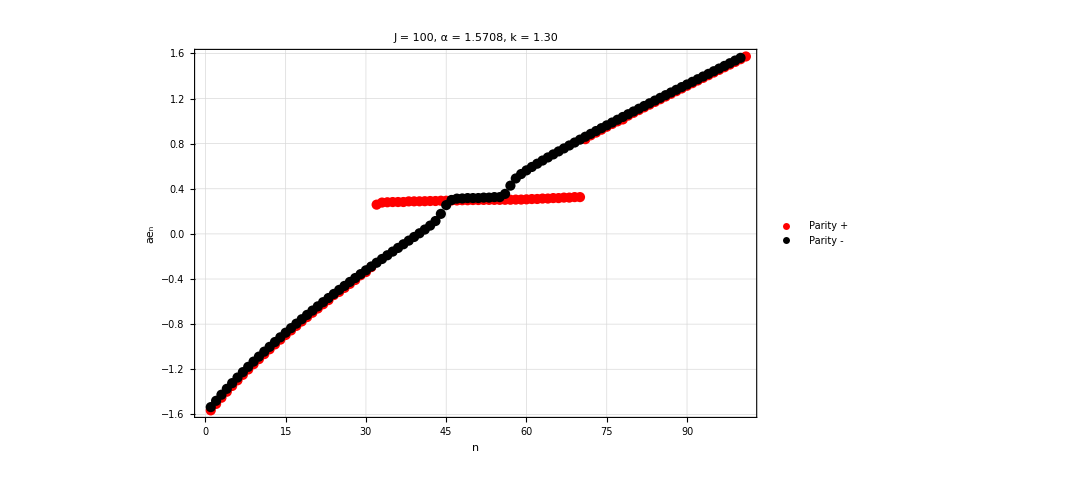

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->800,PlotRange->All]
```

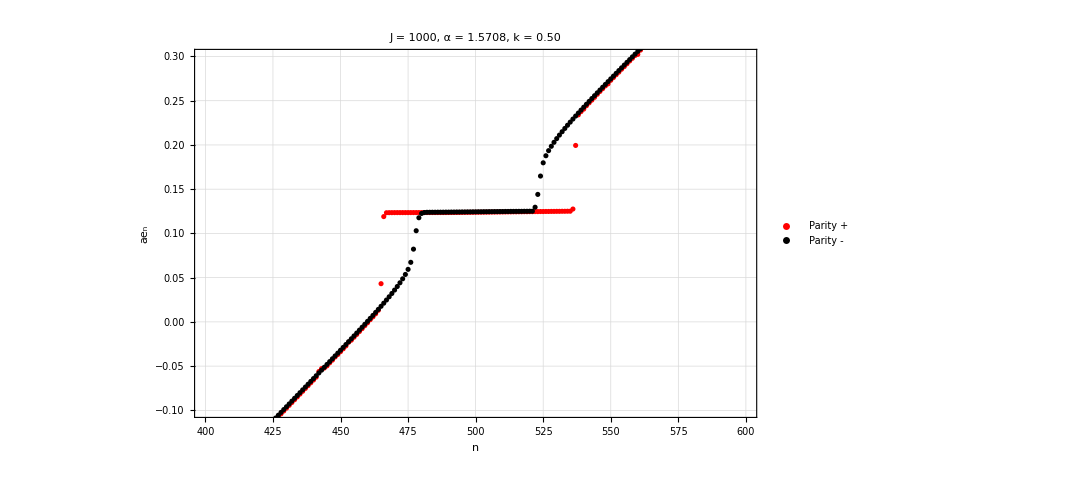

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->800,PlotRange->{{400,600},{-0.1,0.3}}]
```

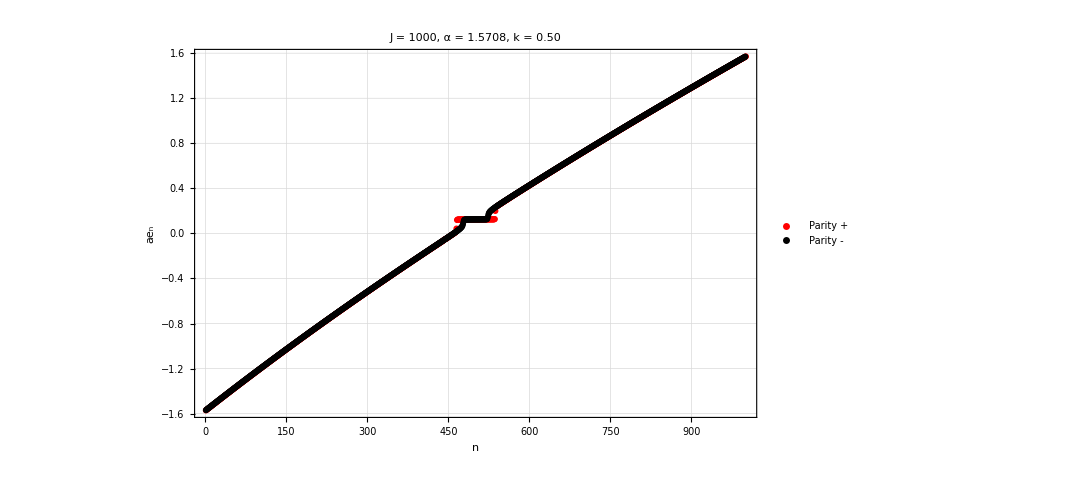

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->800]
```

```mathematica
Export["test1ae.png",plot,ImageResolution->300]
```

test1ae.png

```mathematica
newM=Sort[Chop[szExpectationsM]];
newm=Sort[Chop[szExpectationsm]];
```

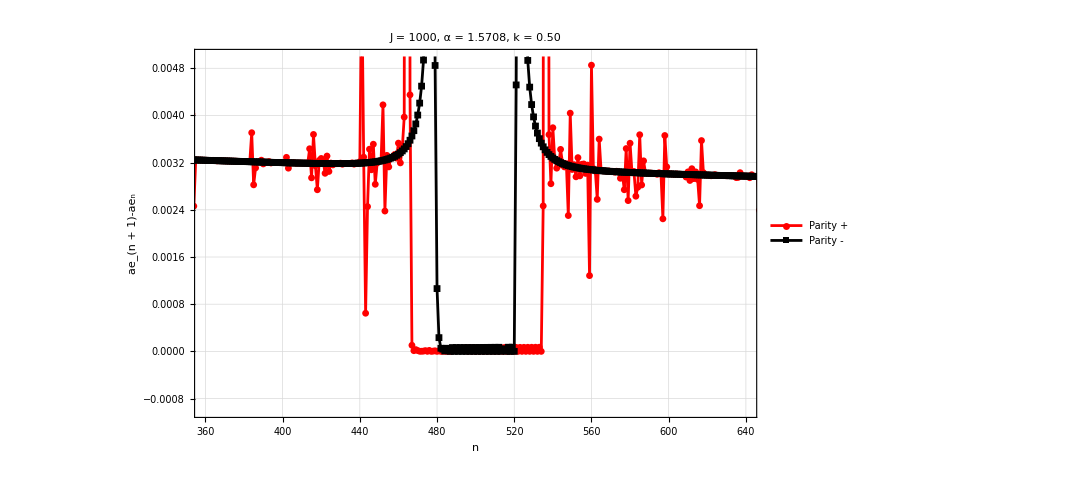

```mathematica
plot2=ListPlot[{Differences[newM],Differences[newm]},PlotStyle->{Red,Black},PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Style["ae_(n + 1)-ae_n",35,Black]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},Joined->True,PlotMarkers->{Automatic, Small},ImageSize->800,PlotRange->{{360,640},{-0.001,0.005}}]
```

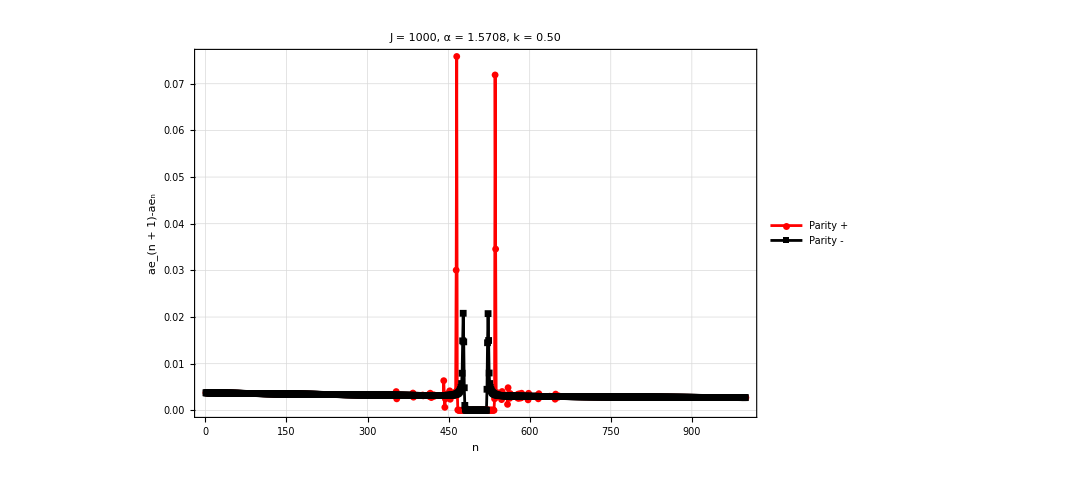

```mathematica
plot2=ListPlot[{Differences[newM],Differences[newm]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Style["ae_(n + 1)-ae_n",35,Black]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},Joined->True,PlotMarkers->{Automatic, Small},ImageSize->800]
```

```mathematica
Export["test2ae.png",plot2,ImageResolution->300]
```

test2ae.png

```mathematica
Export["test3ae.png",plot3,ImageResolution->300]
```

test3ae.png

## Husimis

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Vop;
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
radius=2;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{31397,2}

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 31397 points...

```mathematica
sz=Vop;
ae=Chop[Map[#.sz.ConjugateTranspose[#]&,neweigenvec]];
```

```mathematica
ordering=Ordering[ae];
(*Sort eigenvectors and expectations accordingly*)
eigenvecsSorted=neweigenvec[[ordering]];
eigenvalSorted=neweigenval[[ordering]];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[eigenvecsSorted].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂ of V, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,Background->White]
```

```mathematica
Export["test4ae.png",plot,ImageResolution->300]
```

test4ae.png

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
husimiValues=Abs[overlaps]^2;
husimiValuesSorted=husimiValues;
```

```mathematica
(*Set parameters*)
numEigenstates=2J+1; 
(*should be 2J+1*)
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,husimiValuesSorted[[q]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["AE Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"AE_Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];
plot],{q,2J+1}];
```

# Spectrum Hf as a function of k, α = 0.84

```mathematica
(*Floquet parameters*)
J=40;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
α=0.84;
```

```mathematica
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
(*F[α_,k_] := U0[α].Uk[ k];*)
F[α_,k_] := Uk[k].U0[α];
```

```mathematica
Clear[V];
V[α_,k_]:=(k/(2J))ConjugateTranspose[U0[α]].ops[[4]].U0[α]+α*ops[[3]];
```

```mathematica
alist=Range[0.1,50.,0.02];
alist//Length
```

2496

```mathematica
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
```

```mathematica
DistributeDefinitions[Floq,J,k,MeanLevelSpacingRatio,V,zerosM,zerosm];
```

```mathematica
resultsae=ParallelTable[Module[{mat,matM,matm,valM,valm,eigenvalM,eigenvalm,neweigenvecM,neweigenvecm,Vop,szM,szm,szExpectationsM,szExpectationsm,eigenvecM,eigenvecm},
mat=F[α,a];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];

Vop=V[α,a];
szM=(Vop)[[1;; ;;2,1;; ;;2]];
szm=(Vop)[[2;; ;;2,2;; ;;2]];
szExpectationsM=Map[#.szM.ConjugateTranspose[#]&,eigenvecM];
szExpectationsm=Map[#.szm.ConjugateTranspose[#]&,eigenvecm];

{Transpose[{ConstantArray[a,Length[szExpectationsM]],Sort[szExpectationsM]}],Transpose[{ConstantArray[a,Length[szExpectationsm]],Sort[szExpectationsm]}]}],{a,alist},Method->"CoarsestGrained" ];
{levelsMae,levelsmae}=Transpose[Chop[resultsae]];
```

```mathematica
plot=ListPlot[{Flatten[levelsmae,1],Flatten[levelsMae,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ae",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
Export["plot_alpha_0.84_J_"<>ToString[J]<>"_.png",plot];
```

-Graphics-

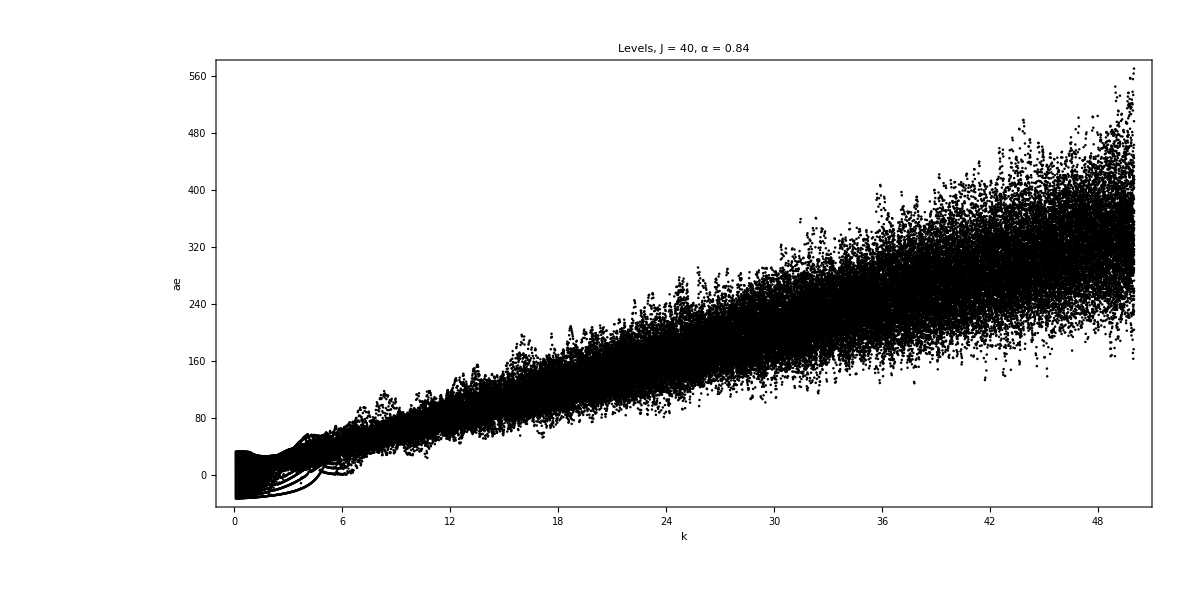

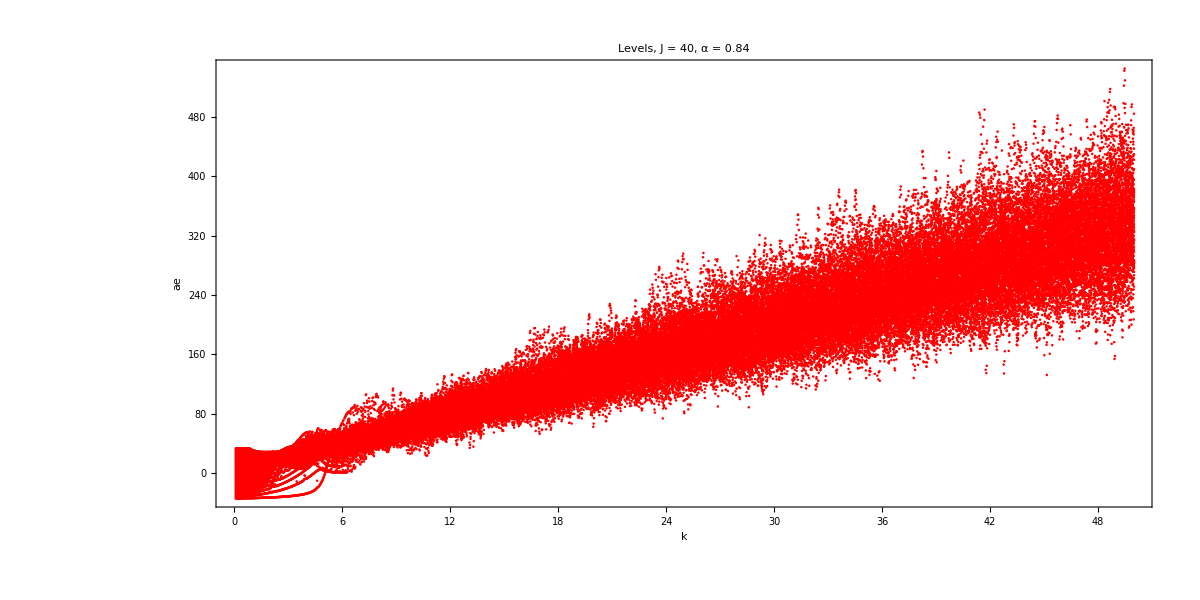

```mathematica
plot=ListPlot[{Flatten[levelsmae,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ae",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
Export["plotM_alpha_0.84_J_"<>ToString[J]<>"_.png",plot];
ListPlot[{Flatten[levelsMae,1]},PlotStyle->{Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ae",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
Export["plotm_alpha_0.84_J_"<>ToString[J]<>"_.png",plot];
```

## Quasienergies

```mathematica
resultsphi=ParallelTable[Module[{mat,matM,matm,valM,valm},
mat=Floq[J,α,a];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
valM=Eigenvalues[matM];
valm=Eigenvalues[matm];
{Transpose[{ConstantArray[a,Length[valM]],Arg[valM]}],Transpose[{ConstantArray[a,Length[valm]],Arg[valm]}]}],{a,alist},Method->"CoarsestGrained" ];
{levelsM,levelsm}=Transpose[resultsphi];
```

```mathematica
plot=ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ϕ",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
Export["quasienergies_alpha_0.84_J_"<>ToString[J]<>"_.png",plot];
```

-Graphics-

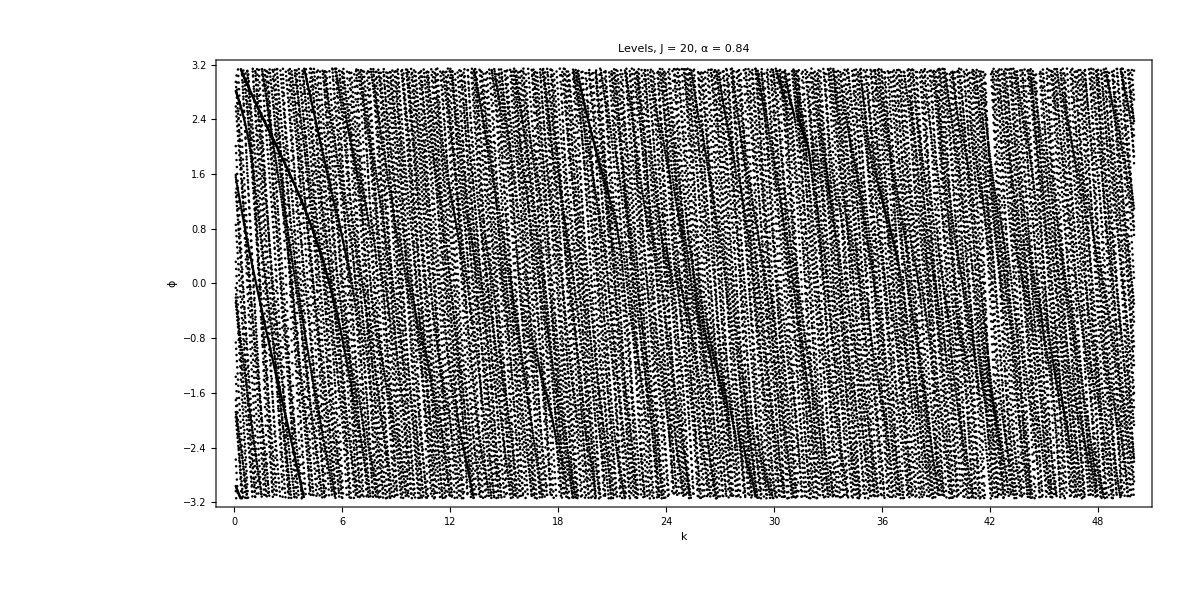

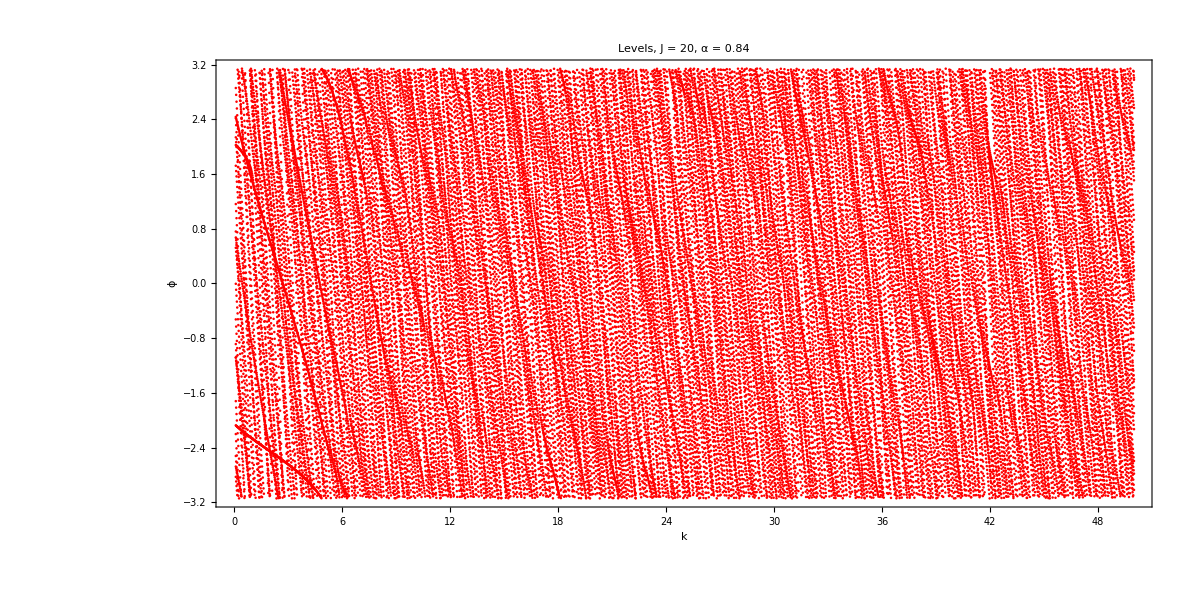

```mathematica
plot=ListPlot[{Flatten[levelsm,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ϕ",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
Export["quasienergiesM_J_"<>ToString[J]<>"_.png",plot];
plot=ListPlot[{Flatten[levelsM,1]},PlotStyle->{Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ϕ",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
Export["quasienergiesm_J_"<>ToString[J]<>"_.png",plot];
```

## Berry phases

```mathematica
(*Calculate Berry Phases by combining AE and Quasienergy calculations*)
resultsBerry=ParallelTable[Module[{mat,matM,matm,valM,valm,eigenvecM,eigenvecm,Vop,szM,szm,aeM,aem,qeM,qem,berryM,berrym},
mat=F[α,a];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
(*Get both eigenvalues and eigenvectors simultaneously to ensure they match*)
{valM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{valm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
Vop=V[α,a];
szM=(Vop)[[1;; ;;2,1;; ;;2]];
szm=(Vop)[[2;; ;;2,2;; ;;2]];
(*1. Calculate average energies (ae) for each eigenstate*)
aeM=Chop[Map[#.szM.ConjugateTranspose[#]&,eigenvecM]];
aem=Chop[Map[#.szm.ConjugateTranspose[#]&,eigenvecm]];
(*2. Calculate quasienergies (qe) for the corresponding eigenstates*)
qeM=Arg[valM];
qem=Arg[valm];
(*3. Calculate Berry phases:Mod[ae-qe,2*Pi]*)(*Note:If you prefer the phase to be wrapped between-Pi and Pi,you can use Mod[aeM-qeM,2 Pi,-Pi] instead*)
berryM=Mod[aeM-qeM,2 Pi];
berrym=Mod[aem-qem,2 Pi];
(*4. Pair with the parameter'a' and sort the Berry phases for clean plotting*)
{Transpose[{ConstantArray[a,Length[berryM]],Sort[berryM]}],Transpose[{ConstantArray[a,Length[berrym]],Sort[berrym]}]}],{a,alist},Method->"CoarsestGrained"];
```

```mathematica
(*Extract the two symmetry sectors*)
{levelsMBerry,levelsmBerry}=Transpose[Chop[resultsBerry]];
```

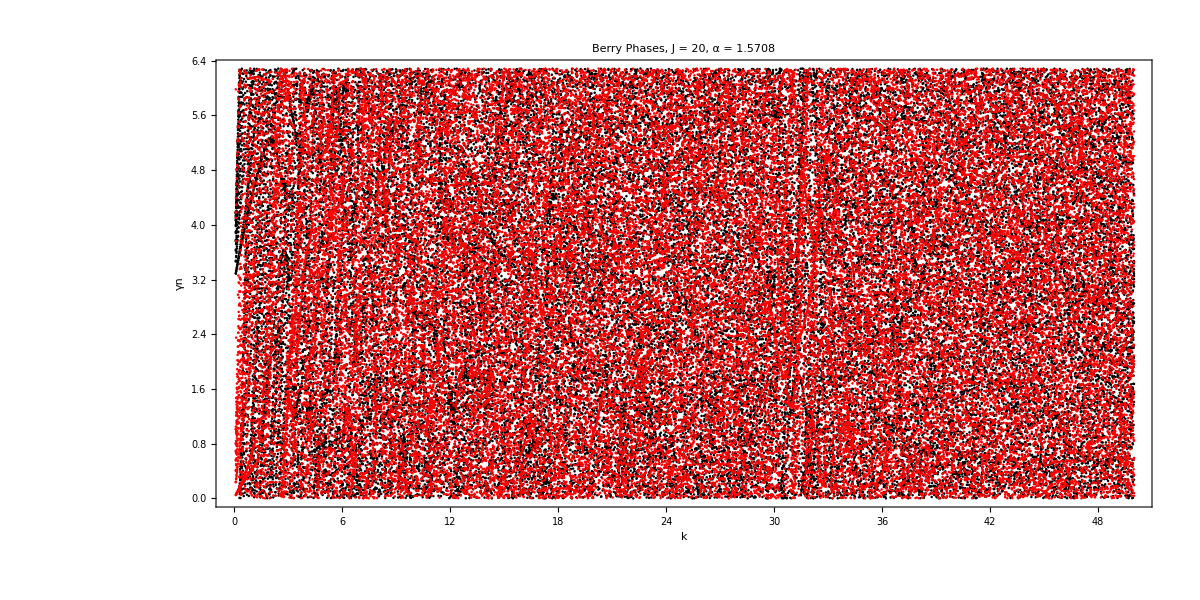

```mathematica
(*Plot the Berry Phases*)
ListPlot[{Flatten[levelsmBerry,1],Flatten[levelsMBerry,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["γn",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Berry Phases, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

# Spectrum Hf as a function of k, α = π/2

```mathematica
(*Floquet parameters*)
J=21;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
α=Pi/2.;
```

```mathematica
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
(*F[α_,k_] := U0[α].Uk[ k];*)
F[α_,k_] := Uk[k].U0[α];
```

```mathematica
Clear[V];
V[α_,k_]:=(k/(2J))ConjugateTranspose[U0[α]].ops[[4]].U0[α]+α*ops[[3]];
```

```mathematica
alist=Range[0.1,6.,0.005];
alist//Length
```

1181

```mathematica
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
```

```mathematica
DistributeDefinitions[Floq,J,k,MeanLevelSpacingRatio,V,zerosM,zerosm];
```

```mathematica
resultsae=ParallelTable[Module[{mat,matM,matm,valM,valm,eigenvalM,eigenvalm,neweigenvecM,neweigenvecm,Vop,szM,szm,szExpectationsM,szExpectationsm,eigenvecM,eigenvecm},
mat=F[α,a];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];

Vop=V[α,a];
szM=(Vop)[[1;; ;;2,1;; ;;2]];
szm=(Vop)[[2;; ;;2,2;; ;;2]];
szExpectationsM=Map[#.szM.ConjugateTranspose[#]&,eigenvecM];
szExpectationsm=Map[#.szm.ConjugateTranspose[#]&,eigenvecm];

{Transpose[{ConstantArray[a,Length[szExpectationsM]],Sort[szExpectationsM]}],Transpose[{ConstantArray[a,Length[szExpectationsm]],Sort[szExpectationsm]}]}],{a,alist},Method->"CoarsestGrained" ];
{levelsMae,levelsmae}=Transpose[Chop[resultsae]];
```

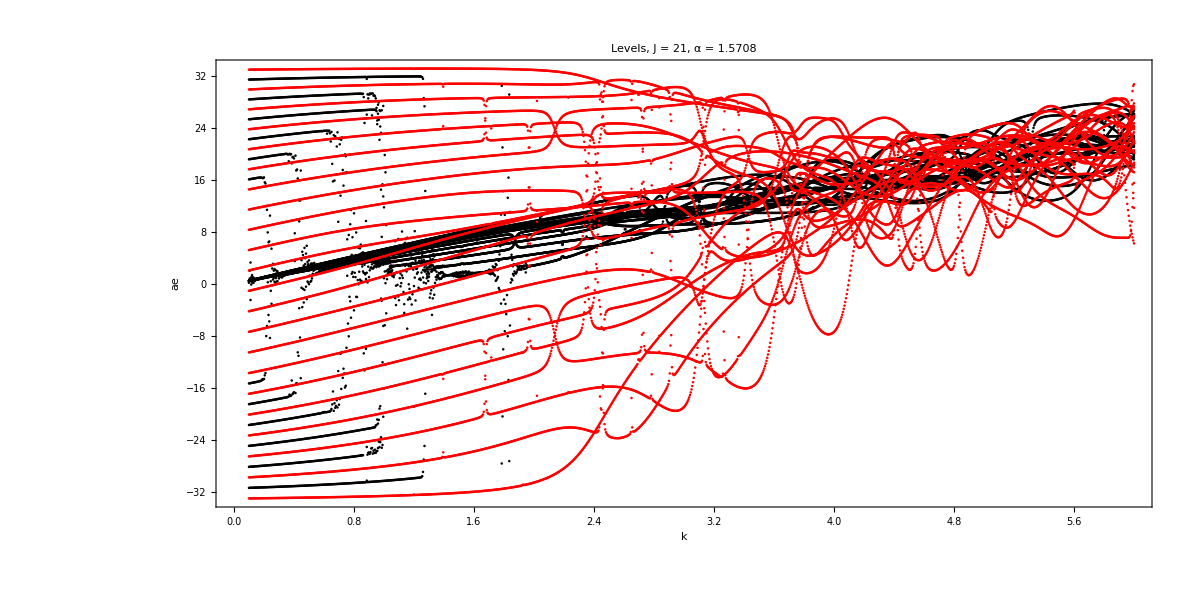

```mathematica
plot=ListPlot[{Flatten[levelsmae,1],Flatten[levelsMae,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ae",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
Export["plot_alpha_halfpi_J_"<>ToString[J]<>"_.png",plot];
```

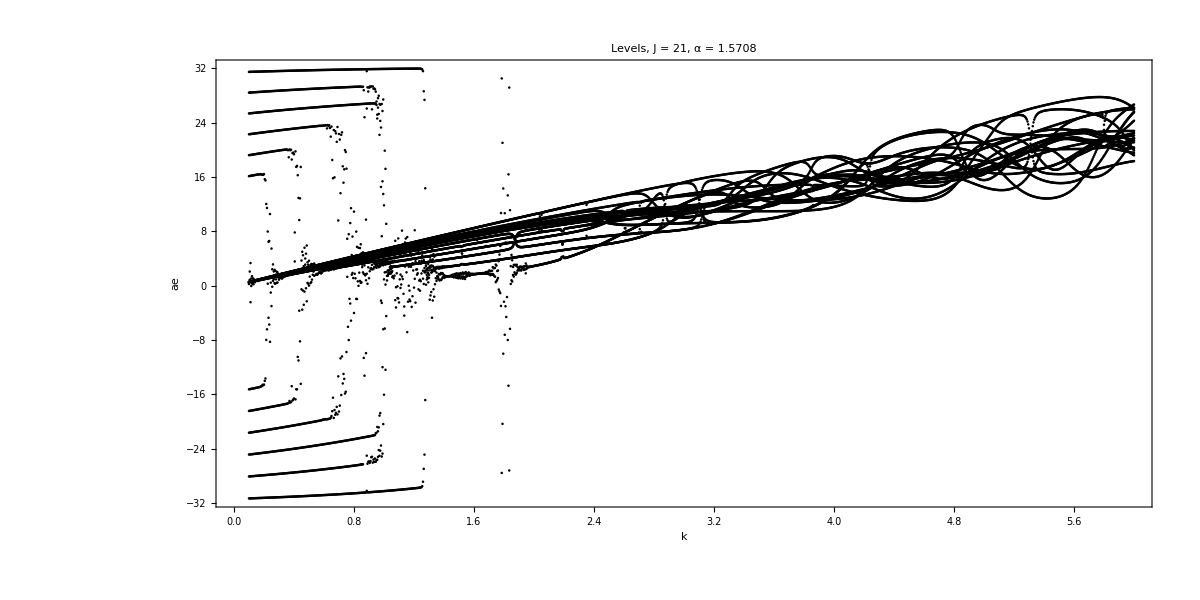

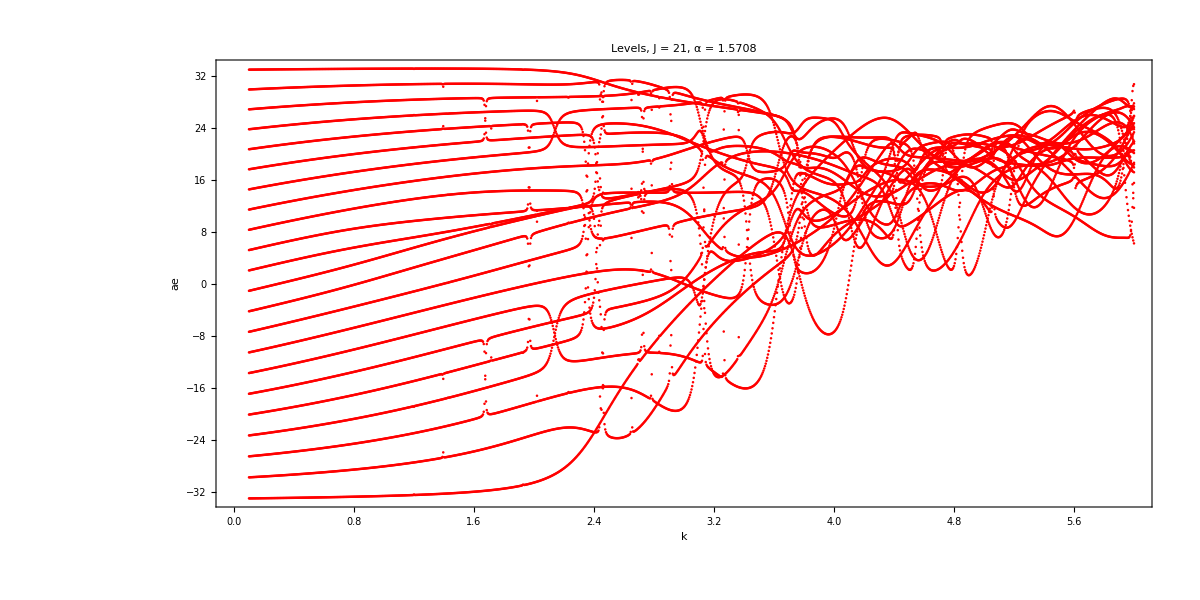

```mathematica
plot=ListPlot[{Flatten[levelsmae,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ae",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
Export["plotM_alpha_halfpi_J_"<>ToString[J]<>"_.png",plot];
ListPlot[{Flatten[levelsMae,1]},PlotStyle->{Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ae",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
Export["plotm_alpha_halfpi_J_"<>ToString[J]<>"_.png",plot];
```

## Quasienergies

```mathematica
resultsphi=ParallelTable[Module[{mat,matM,matm,valM,valm},
mat=Floq[J,α,a];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
valM=Eigenvalues[matM];
valm=Eigenvalues[matm];
{Transpose[{ConstantArray[a,Length[valM]],Arg[valM]}],Transpose[{ConstantArray[a,Length[valm]],Arg[valm]}]}],{a,alist},Method->"CoarsestGrained" ];
{levelsM,levelsm}=Transpose[resultsphi];
```

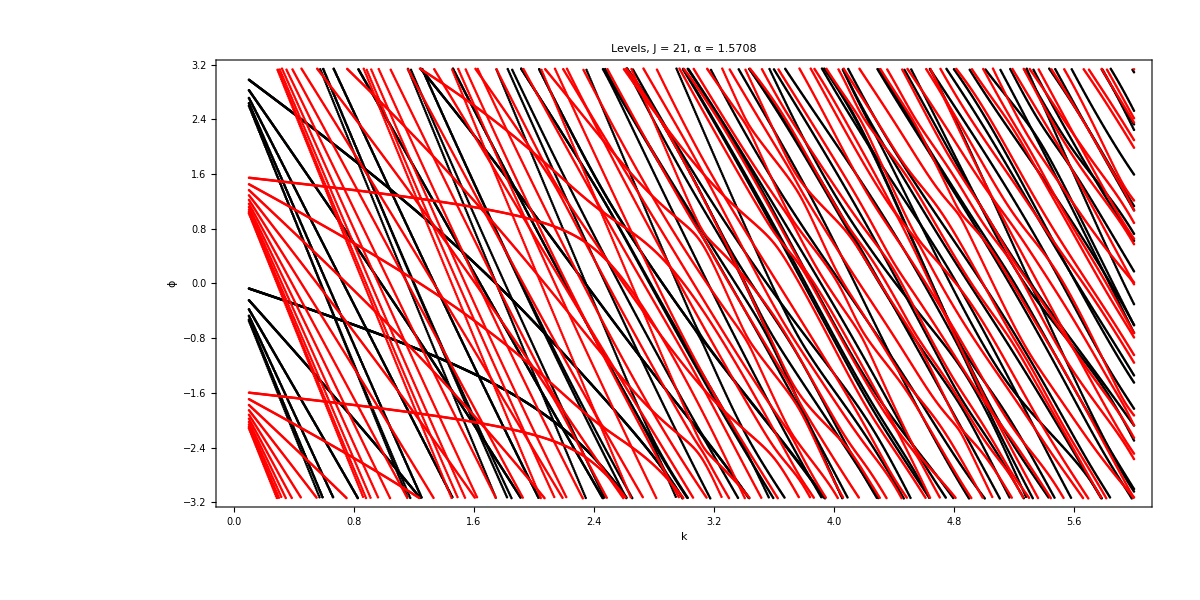

```mathematica
plot=ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ϕ",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
Export["quasienergies_alpha_halfpi_J_"<>ToString[J]<>"_.png",plot];
```

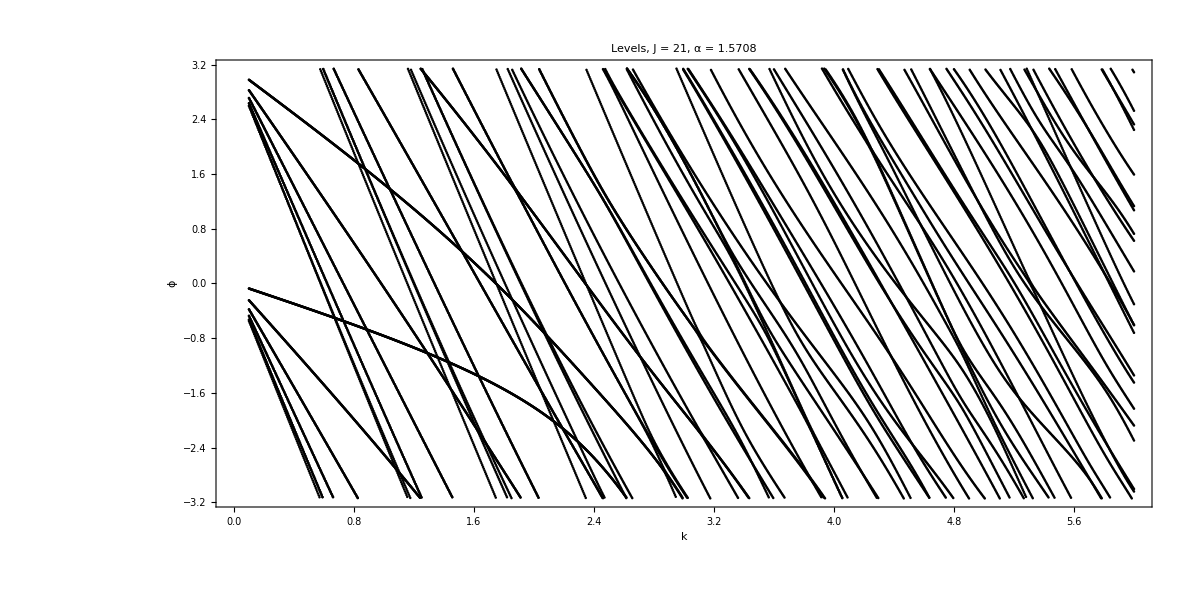

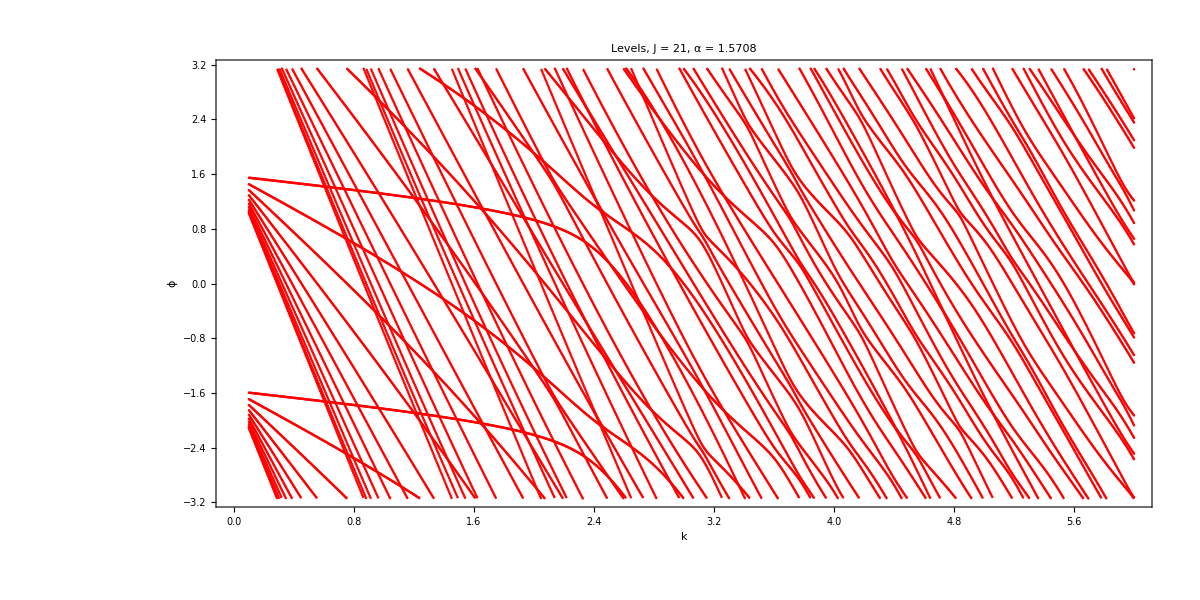

```mathematica
plot=ListPlot[{Flatten[levelsm,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ϕ",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
Export["quasienergiesM_alpha_halfpi_J_"<>ToString[J]<>"_.png",plot];
plot=ListPlot[{Flatten[levelsM,1]},PlotStyle->{Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ϕ",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
Export["quasienergiesm_alpha_halfpi_J_"<>ToString[J]<>"_.png",plot];
```

## Berry phases

```mathematica
(*Calculate Berry Phases by combining AE and Quasienergy calculations*)
resultsBerry=ParallelTable[Module[{mat,matM,matm,valM,valm,eigenvecM,eigenvecm,Vop,szM,szm,aeM,aem,qeM,qem,berryM,berrym},
mat=F[α,a];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
(*Get both eigenvalues and eigenvectors simultaneously to ensure they match*)
{valM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{valm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
Vop=V[α,a];
szM=(Vop)[[1;; ;;2,1;; ;;2]];
szm=(Vop)[[2;; ;;2,2;; ;;2]];
(*1. Calculate average energies (ae) for each eigenstate*)
aeM=Chop[Map[#.szM.ConjugateTranspose[#]&,eigenvecM]];
aem=Chop[Map[#.szm.ConjugateTranspose[#]&,eigenvecm]];
(*2. Calculate quasienergies (qe) for the corresponding eigenstates*)
qeM=Arg[valM];
qem=Arg[valm];
(*3. Calculate Berry phases:Mod[ae-qe,2*Pi]*)(*Note:If you prefer the phase to be wrapped between-Pi and Pi,you can use Mod[aeM-qeM,2 Pi,-Pi] instead*)
berryM=Mod[aeM-qeM,2 Pi];
berrym=Mod[aem-qem,2 Pi];
(*4. Pair with the parameter'a' and sort the Berry phases for clean plotting*)
{Transpose[{ConstantArray[a,Length[berryM]],Sort[berryM]}],Transpose[{ConstantArray[a,Length[berrym]],Sort[berrym]}]}],{a,alist},Method->"CoarsestGrained"];
```

```mathematica
(*Extract the two symmetry sectors*)
{levelsMBerry,levelsmBerry}=Transpose[Chop[resultsBerry]];
```

```mathematica
(*Plot the Berry Phases*)
ListPlot[{Flatten[levelsmBerry,1],Flatten[levelsMBerry,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["γn",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Berry Phases, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

-Graphics-

# Spectrum Hf as a function α

```mathematica
(*Floquet parameters*)
J=51;
```

```mathematica
k=1.3;
```

```mathematica
alist=Range[0,2Pi,Pi/1000];
alist//Length
```

2001

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
```

```mathematica
DistributeDefinitions[Floq,J,k,MeanLevelSpacingRatio,V,zerosM,zerosm];
```

```mathematica
resultsae=ParallelTable[Module[{mat,matM,matm,valM,valm,eigenvalM,eigenvalm,neweigenvecM,neweigenvecm,Vop,szM,szm,szExpectationsM,szExpectationsm,eigenvecM,eigenvecm},
mat=Floq[J,a,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];

Vop=V[a,k];
szM=(Vop)[[1;; ;;2,1;; ;;2]];
szm=(Vop)[[2;; ;;2,2;; ;;2]];
szExpectationsM=Map[#.szM.ConjugateTranspose[#]&,eigenvecM];
szExpectationsm=Map[#.szm.ConjugateTranspose[#]&,eigenvecm];

{Transpose[{ConstantArray[a,Length[szExpectationsM]],Sort[szExpectationsM]}],Transpose[{ConstantArray[a,Length[szExpectationsm]],Sort[szExpectationsm]}]}],{a,alist},Method->"CoarsestGrained" ];
```

```mathematica
CustomPiTicks[d_]:=Table[{k*Pi/d,If[k==0,"0",If[k==d,"",Row[{Rationalize[k/d],""}]]]},{k,0,2d+1}];
(*Generate ticks for Pi/20*)
myTicks=CustomPiTicks[10];
```

```mathematica
{levelsMae,levelsmae}=Transpose[Chop[resultsae]];
ListPlot[{Flatten[levelsmae,1],Flatten[levelsMae,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["α/π",30,Black],Style["ae",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = "<>ToString[k]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

-Graphics-

```mathematica
{levelsMae,levelsmae}=Transpose[Chop[resultsae]];
ListPlot[{Flatten[levelsmae,1],Flatten[levelsMae,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["α/π",30,Black],Style["ae",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = "<>ToString[k]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

-Graphics-

## Quasienergies

```mathematica
resultsphi=ParallelTable[Module[{mat,matM,matm,valM,valm},
mat=Floq[J,a,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
valM=Eigenvalues[matM];
valm=Eigenvalues[matm];
{Transpose[{ConstantArray[a,Length[valM]],Arg[valM]}],Transpose[{ConstantArray[a,Length[valm]],Arg[valm]}]}],{a,alist},Method->"CoarsestGrained" ];
{levelsM,levelsm}=Transpose[resultsphi];
```

```mathematica
ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["α",30,Black],Style["ae",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = "<>ToString[k]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

-Graphics-

## Berry phases

```mathematica
(*Calculate Berry Phases by combining AE and Quasienergy calculations*)
resultsBerry=ParallelTable[Module[{mat,matM,matm,valM,valm,eigenvecM,eigenvecm,Vop,szM,szm,aeM,aem,qeM,qem,berryM,berrym},
mat=Floq[J,a,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
(*Get both eigenvalues and eigenvectors simultaneously to ensure they match*)
{valM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{valm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
Vop=V[a,k];
szM=(Vop)[[1;; ;;2,1;; ;;2]];
szm=(Vop)[[2;; ;;2,2;; ;;2]];
(*1. Calculate average energies (ae) for each eigenstate*)
aeM=Chop[Map[#.szM.ConjugateTranspose[#]&,eigenvecM]];
aem=Chop[Map[#.szm.ConjugateTranspose[#]&,eigenvecm]];
(*2. Calculate quasienergies (qe) for the corresponding eigenstates*)
qeM=Arg[valM];
qem=Arg[valm];
(*3. Calculate Berry phases:Mod[ae-qe,2*Pi]*)(*Note:If you prefer the phase to be wrapped between-Pi and Pi,you can use Mod[aeM-qeM,2 Pi,-Pi] instead*)
berryM=Mod[aeM-qeM,2 Pi];
berrym=Mod[aem-qem,2 Pi];
(*4. Pair with the parameter'a' and sort the Berry phases for clean plotting*)
{Transpose[{ConstantArray[a,Length[berryM]],Sort[berryM]}],Transpose[{ConstantArray[a,Length[berrym]],Sort[berrym]}]}],{a,alist},Method->"CoarsestGrained"];
```

```mathematica
(*Extract the two symmetry sectors*)
{levelsMBerry,levelsmBerry}=Transpose[Chop[resultsBerry]];
```

```mathematica
(*Plot the Berry Phases*)
ListPlot[{Flatten[levelsmBerry,1],Flatten[levelsMBerry,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["α",30,Black],Style["γn",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Berry Phases, J = ",J,", k = "<>ToString[k]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

-Graphics-

# Parity separation

```mathematica
Print["Computing Floquet matrix..."];
J=501;
α=Pi/2.;
k=10.;
Clear[mat];
mat=Floq[J,α,k];
d=2 J+1;
```

Computing Floquet matrix...

```mathematica
(*1. Dynamically determine indices based on the actual m quantum number*)
mValues=Range[J,-J,-1];
```

```mathematica
If[IntegerQ[J],(*For Integer J,explicitly hunt down the Even and Odd m states*)
idxEvenM=Flatten@Position[mValues,m_/;EvenQ[m]];
idxOddM=Flatten@Position[mValues,m_/;OddQ[m]];,
(*For Half-Integer J,m is fractional.Default to standard decoupled alternating sets*)
idxEvenM=Range[1,d,2];
idxOddM=Range[2,d,2];];
```

```mathematica
(*2. Extract the submatrices based on the physical indices*)
matEven=mat[[idxEvenM,idxEvenM]];
matOdd=mat[[idxOddM,idxOddM]];
```

```mathematica
(*3. Diagonalize both sectors*)
{eigenvalEven,eigenvecEven}=Eigensystem[matEven,Method->"Direct"];
{eigenvalOdd,eigenvecOdd}=Eigensystem[matOdd,Method->"Direct"];
```

```mathematica
(*4. Reconstruct full eigenvectors robustly (No more Riffle!)*)
neweigenvecEven=Table[vec=ConstantArray[0.,d];
vec[[idxEvenM]]=eigenvecEven[[j]];
vec,{j,Length[idxEvenM]}];

neweigenvecOdd=Table[vec=ConstantArray[0.,d];
vec[[idxOddM]]=eigenvecOdd[[j]];
vec,{j,Length[idxOddM]}];
```

```mathematica
(*5. Combine the final spectrum*)
neweigenvec=Join[neweigenvecEven,neweigenvecOdd];
neweigenval=Join[eigenvalEven,eigenvalOdd];
```

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalEven]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalOdd]]]}
```

{0.425479,0.498472}

```mathematica
phases=Sort[Arg[eigenvalEven]];
data=Table[{phases[[i]],i},{i,1,Length[phases]}];
```

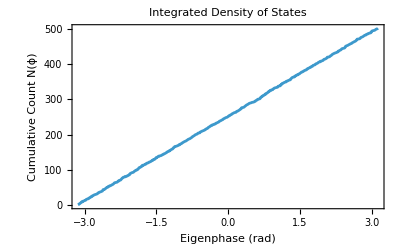

```mathematica
(*3. Plot the staircase function*)
ListPlot[data,Frame->True,FrameLabel->{"Eigenphase (rad)","Cumulative Count N(ϕ)"},PlotLabel->"Integrated Density of States",Joined->True]
```

```mathematica
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
poisson[s_]:=Exp[-s];
wignerDyson[s_]:=(Pi*s/2)*Exp[-(Pi*s^2)/4];
```

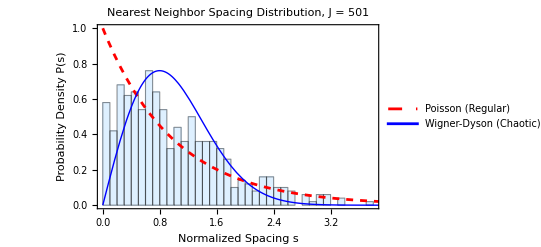

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

# Parity separation

```mathematica
Print["Computing Floquet matrix..."];
J=100;
α=Pi/2.;
k=10.;
Clear[mat];
mat=Floq[J,α,k];
d=2 J+1;
```

Computing Floquet matrix...

```mathematica
(*1. Fast,Universal Parity Sector Separation*)
(*Sx^2 strictly couples m to m±2,meaning alternating array indices ALWAYS decouple.*)
If[IntegerQ[J]&&OddQ[J],
(*If J is an odd integer,the highest m (index 1) is odd.Thus,index 2 starts the Even m sector.*)idxEvenM=Range[2,d,2];
idxOddM=Range[1,d,2];,
(*If J is an even integer,the highest m (index 1) is even.*)(*If J is a half-integer,'Even/Odd' m doesn't exist,so we default to standard decoupling.*)idxEvenM=Range[1,d,2];
idxOddM=Range[2,d,2];];
```

```mathematica
(*2. Extract the submatrices based on the physical indices*)
matEven=mat[[idxEvenM,idxEvenM]];
matOdd=mat[[idxOddM,idxOddM]];
```

```mathematica
(*3. Diagonalize both sectors*)
{eigenvalEven,eigenvecEven}=Eigensystem[matEven,Method->"Direct"];
{eigenvalOdd,eigenvecOdd}=Eigensystem[matOdd,Method->"Direct"];
```

```mathematica
(*4. Reconstruct full eigenvectors robustly*)
neweigenvecEven=Table[vec=ConstantArray[0.,d];
vec[[idxEvenM]]=eigenvecEven[[j]];
vec,{j,Length[idxEvenM]}];

neweigenvecOdd=Table[vec=ConstantArray[0.,d];
vec[[idxOddM]]=eigenvecOdd[[j]];
vec,{j,Length[idxOddM]}];
```

```mathematica
(*5. Combine the final spectrum*)
neweigenvec=Join[neweigenvecEven,neweigenvecOdd];
neweigenval=Join[eigenvalEven,eigenvalOdd];
```

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalEven]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalOdd]]]}
```

{0.514199,0.51472}

```mathematica
phases=Sort[Arg[eigenvalEven]];
phases=Sort[Arg[eigenvalOdd]];
data=Table[{phases[[i]],i},{i,1,Length[phases]}];
```

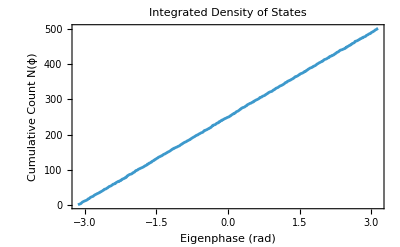

```mathematica
(*3. Plot the staircase function*)
ListPlot[data,Frame->True,FrameLabel->{"Eigenphase (rad)","Cumulative Count N(ϕ)"},PlotLabel->"Integrated Density of States",Joined->True]
```

```mathematica
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
poisson[s_]:=Exp[-s];
wignerDyson[s_]:=(Pi*s/2)*Exp[-(Pi*s^2)/4];
```

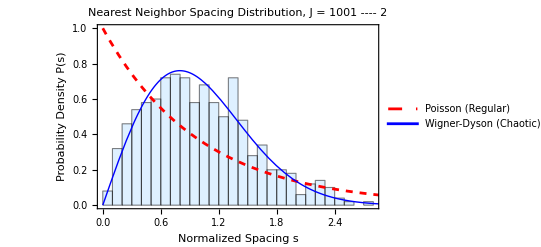

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```